## Resolver la Ecuación de Schrodinger estacionaria

Sabemos que un electrón o fotón, por ejemplo, cumple la dualidad onda-partícula de la mecánica cuántica, gracias a las ecuaciones de Schrodinger y de Klein-Gordan.

Al final, añadiendo un potencial independiente del tiempo, y en el caso estacionario, la ecuación a Schrodinger a resolver será:
-ℏ/2m *ϕ’’_n(x) + V(x) ϕ_n(x)=E_n ϕ_n (x)

### Potencial

Comencemos definiendo el potencial, que será el de una caja:

```mathematica
a=1;
h=1;
```

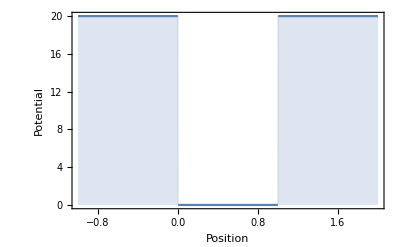

```mathematica
width=1;
V0=20;
V[x_]:=V0*(Sign[-x]+1)/2+V0*(Sign[x-a]+1)/2
potPlot=Plot[V[x],{x,-1,2},Axes->False,Frame->True,FrameLabel->{"Position","Potential"},Filling->Bottom]
```

### Hamiltoniano

Con el potencial, pasemos a definir el Hamiltoniano H|ϕ>=E|ϕ>:

```mathematica
const=-0.03; (*es -hbar^2/2m*)
left=const*phi''[x]+V[x]*phi[x]
```

phi[x] (10 (1+Sign[-1+x])+10 (1-Sign[x]))-0.03 phi''[x]

### Determinar el sistema propio (eigensystem)

```mathematica
{vals,fun}=NDEigensystem[left,phi[x],{x,-0.5,1.5},9]
```

{{0.255615,1.02142,2.29491,4.07358,6.35627,9.14241,12.4247,16.1573,19.897},{InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x]}}

Es decir, es súper fuerte lo que hemos conseguido. En una sola línea de código, hemos obtenido los autovalores y autofunciones del sistema, en el intervalo -0.5 y 1.5.

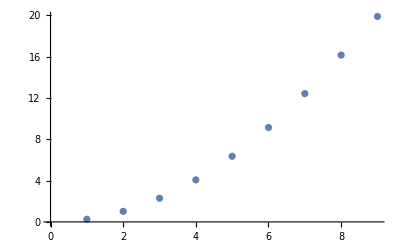

```mathematica
ListPlot[vals]
```

Si hubiera valores por encima de 20, que sería por encima del potencial, no tendrían sentido físico (esto pasa si en vez de 9 soluciones buscamos más, por ejemplo 15), que se descartarían.

Y podemos ver también la forma de las funciones, tal que en orden, cada uno de ellos, cortará más y más veces al eje: es lo que se espera de los estados excitados, que el 2 corte 2 veces:

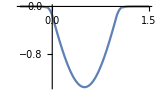
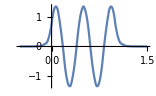
Grid[-Graphics-,-Graphics-]

```mathematica
Grid[
	Plot[Evaluate[fun[[1]]],{x,-0.5,1.5}], (*estado fundamental, n=0*)
	Plot[Evaluate[fun[[5]]],{x,-0.5,1.5}] (*4 estado excitado, n=4*)
	]
```

Podríamos meter estos potenciales en el perfil del potencial para hacer los típicos plots del estado fundamental y los excitados dentro de una caja:

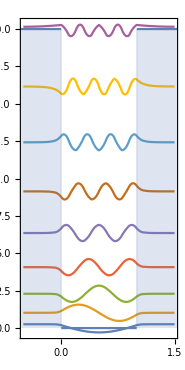

```mathematica
Show[
	Plot[Evaluate[0.4*fun+vals],{x,-0.5,1.5},AspectRatio->2,Axes->False,Frame->True],
	potPlot
]
```

Por ejemplo, el morado de arriba del todo no tiene sentido físico porque se encuentra por encima de la caja. Esto es porque ya no será una solución estacionaria dentro de la caja, y no tiene sentido que sea por ende una solución. Para quitarla, tomamos donde dijimos antes 8 en vez de 9.

Entonces vemos claramente la naturaleza ondulatoria de la partícula. La probabilidad de encontrar la partícula en cada estado será el cuadrado de la solución:

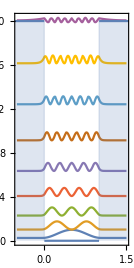

```mathematica
Show[
	Plot[Evaluate[0.4*Abs[fun]^2+vals],{x,-0.5,1.5},AspectRatio->2,Axes->False,Frame->True],
	potPlot
]
```

El estado fundamental, por ejemplo, es muy probable encontrar la partícula en el centro, mientras que en el primer estado excitado será más posible en dos lugares: otro comportamiento puramente cuántico, ya que no tiene una localización definida hasta que la medimos.

Para ver si la función está normalizada, tenemos que integrar en todo el dominio espacial, que en esta caso será entre -0.5 y 1.5:

```mathematica
NIntegrate[Abs[fun]^2,{x,-0.5,1.5}]
```

{1.,1.,1.,1.,0.999998,0.999997,1.,0.999999,0.999999}

Obteniéndose en todos un valor=1 (no sale exactamente 1 porque puede ser muy difícil de integrar, acuérdate de Física Cuántica, que necesitabas tablas y cosas difíciles para resolver esas integrales demoníacas).

## Espín del electrón y Computación cuántica

Con el experimento de Stern-Gerlach, se observó que el espín vive en dos funciones a la vez, descrito por un espinor, teniendo el espín hacia arriba y hacia abajo a la vez, viviendo en una superposición.

No es hasta que decidimos medir el espín que adopta uno de los dos valores posibles, o +1/2 o -1/2, pero si no lo hacemos, vive en esa bonita superposición que nos impide saber cuál será el resultado de la medida.

Este mismo razonamiento se da para los qubits, que se describen por 1 o 0, pero siendo estados cuánticos tal que |1>=(1,0) y |0>=(0,1).

### Espín como un qubit

```mathematica
up={1,0};
down={0,1};
```

Tal que el estado a describir será una superposición de estos dos estados:

```mathematica
psi=α*up+β*down
```

{α,β}

### Valor esperado del espín

Comenzamos definiendo las matrices de Pauli:

```mathematica
sx=PauliMatrix[1];
sy=PauliMatrix[2];
sz=PauliMatrix[3]
```

{{1,0},{0,-1}}

Tal que la orientación de nuestro espinor vendrá dado por:

```mathematica
orientation[psi_]:={Conjugate[psi].sx.psi,Conjugate[psi].sy.psi,Conjugate[psi].sz.psi}
```

Para representar los espinores, usaremos la siguiente función que nos dibuja una esfera en 3D:

```mathematica
blockSphere[psi_]:=Graphics3D[{
	Arrow[{{0,0,0},orientation[psi]}],
	Dashed,Line[{{0,0,0},{1.2,0,0}}],Line[{{0,0,0},{0,1.2,0}}],Line[{{0,0,0},{0,0,1.2}}],
	Text["x",{1.3,0,0}],Text["y",{0,1.3,0}],Text["z",{0,0,1.3}],
	Gray,Opacity[0.2],Sphere[],
	Cylinder[{{0,0,0},{0,0,0.0001}}]
	},
	ViewPoint->{0.8,0.8,1},Boxed->False,Lighting->"Neutral"
	]
```

### Ejemplo

Definamos un espinor complejo:

```mathematica
psiA=Normalize[(1*I)*up+(-2+0.5 I)*down]
```

{0.+0.436436 ⅈ,-0.872872+0.218218 ⅈ}

```mathematica
orientation[psiA]
```

{0.190476+0. ⅈ,0.761905+0. ⅈ,-0.619048+0. ⅈ}

Con la función que habíamos definido antes, veamos en que dirección apunta nuestro espinor:

```mathematica
blockSphere[psiA]
```

-Graphics3D-

Como ya dijimos, esta es la superposición del estado, que ni apunta en (1,0) ni (0,1), y una vez hagamos la medida, colapsará a uno de los dos estados.

### Operación de un sencillo qubit

Los qubit vienen ya incluidos en Mathematica, y podemos acceder a ellas de la siguiente manera:

```mathematica
HadamardMatrix[2]//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
HadamardMatrix[2].up//MatrixForm
```

(1/(√2)
1/(√2))

```mathematica
orientation[HadamardMatrix[2].up]
orientation[HadamardMatrix[2].down]

Grid[blockSphere[HadamardMatrix[2].up],
	blockSphere[HadamardMatrix[2].down]]
```

{1,0,0}

{-1,0,0}

Grid[-Graphics3D-,-Graphics3D-]

Estas matrices las podríamos aplicar sobre las funciones que ya usamos antes para convertir estados puros en estados superpuestos:

```mathematica
blockSphere[HadamardMatrix[2].psiA]
```

-Graphics3D-

### Dos operaciones de qubits

Hagamos una superposición de dos estados:

```mathematica
psi2[psia_,psib_]:={psia[[1]]*psib[[1]],psia[[1]]*psib[[2]],psia[[2]]*psib[[1]],psia[[2]]*psib[[2]]}
```

Y definamos una matriz que nos entrelaza de alguna manera los estados:

```mathematica
cnot={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
cnot//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

### Entrelazamiento

Para llevarlo a cabo, necesitamos dos estados puros, y les aplicamos la matriz anterior:

```mathematica
cnot.psi2[HadamardMatrix[2].up,up] //MatrixForm
```

(1/(√2)
0
0
1/(√2))

Como las dos primeras componentes son del espín up, y las dos de abajo del espín down, está claro que la posibilidad de obtener el valor de cada espín es 1/2.